#### Init:

```mathematica
SetDirectory@NotebookDirectory[];
Import["D-params.m"];
Import["D-nde-funcs.m"];
```

# Looks like the basic structure of the generalized 1D-Polar NDE solver is in place. Now to implement calculating functions

```mathematica
Table[QuantityMagnitude[Quantity[l,"Nanometers"],"BohrRadius"],{l,0.4,0.8,0.05}]
```

{7.5589,8.50377,9.44863,10.3935,11.3384,12.2832,13.2281,14.1729,15.1178}

```mathematica
Module[
{
mu=0.2,chi=13,l=7,kappa=1,rho0=(2*Pi*13/1),z=0,
c=10,shift=1,
tde=(diffeqtransrules["1dp"][diffeqkeop["iso"]+pots["iso","rk"]*f[r]]),
tdenum=With[{mu=0.2,chi=13,l=7,kappa=1,rho0=(2*Pi*13/1),z=0,c=10,shift=1},Evaluate@(diffeqtransrules["1dp"][diffeqkeop["iso"]+pots["iso","rk"]*f[r]])],
nmax=3,
res,evs,efs,esform,evform,efform,tefs,ndestats,
memi,memf,memx,
out,norms,normstats,ntefs,normcheck,normcheckstats,rmax=10^6,
rsq,xbhrad,f0,alpha,afac,alcon,
lc,ldbr,leff,Mcav,Mex,hxsq,hcsq,gamcav,gamcavreff,gampol,exk,eck,ephotpct,elpup,elp,eup,mlpup,exres,vsav,vsavmod,vflat,EfromT,TfromE,U0,Cs,tcpol,tcpol2,critdensfromT,normdens,tcdirect,tcpostsolve,ns,tc0,ncrit,
ndeopts={Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->10^-3}},"Eigensystem"->{"Arnoldi","MaxIterations"->10^12},"VectorNormalization"->None}},
nintopts={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6}
},
(memi=N@UnitConvert[Quantity[MemoryInUse[],"Bytes"],"Gigabytes"]);
(* Solve the Schrodinger equation *)
res=med[Unevaluated[Table[
NDEigensystem[
{
Evaluate[(tdenum/.angm->mind)],
DirichletCondition[g[s]==0,s==Pi/2]
},
g[s],
{s,0,Pi/2},
nmax-mind,
Evaluate@FilterRules[{ndeopts},Options[NDEigensystem]]
],
{mind,0,nmax-1}
]]];
{evs=UnitConvert[Quantity[res[[1,;;,1]]-shift,"Hartrees"],"Millielectronvolts"],(efs=res[[1,;;,2]]),ndestats=res[[2]]};
(* Transform and normalize the EFs *)
tefs=Table[Function[{r},Evaluate[Head[efs[[i,j]]][ArcTan[r/c]]]],{i,nmax},{j,1,nmax+1-i}];
{norms,normstats}=med[Unevaluated[Table[
NIntegrate[
r*(tefs[[i,j]][r])^2,
{r,0,rmax},
Evaluate@FilterRules[{nintopts},Options[NIntegrate]]
],
{i,nmax},{j,1,nmax+1-i}
]]];
ntefs=Table[
Function[{r},Evaluate[tefs[[i,j]][r]/Sqrt[norms[[i,j]]]]],
{i,nmax},{j,1,nmax+1-i}
];
{normcheck,normcheckstats}=med[Unevaluated[Table[
Table[
NIntegrate[r*ntefs[[i,j]][r]*ntefs[[i,jp]][r],{r,0,rmax},Evaluate@FilterRules[{nintopts},Options[NIntegrate]]],
{j,1,nmax+1-i},{jp,1,nmax+1-i}
],
{i,nmax}
]]];
(* Reorganize the EVs and ntEFs to make other calculations more straightforward *)
esform=<|Table[
tssf["`1`,`2`",i,i-j]->{evs[[i-j+1,j]],ntefs[[i-j+1,j]]},
{i,nmax},{j,i,1,-1}
]|>;
evform=Table[evs[[i-j+1,j]],{i,nmax},{j,i,1,-1}];
efform=Table[ntefs[[i-j+1,j]],{i,nmax},{j,i,1,-1}];
rsq=Table[UnitConvert[Quantity[Sqrt[NIntegrate[(r^3)*(efform[[n,m,2]][r])^2,{r,0,rmax},Evaluate@FilterRules[{nintopts},Options[NIntegrate]]]],"BohrRadius"],"Nanometers"],{n,nmax},{m,n}];
xbhrad=Table[UnitConvert[Quantity[NMaximize[{Abs[r*efform[[n,m,2]][r]],0≤r≤3000},r,Method->"SimulatedAnnealing"],"BohrRadius"],"Nanometers"],{n,nmax},{m,n}];
(* EXCITON OPTICAL PROPERTIES *)
f0=Table[(* THIS IS f0 for ONE transition *)
2*QuantityMagnitude[evform[[n,1]]-evform[[1,1]]]*(NIntegrate[r*efform[[1,0]][r]*efform[[n,1]][r],{r,0,rmax},Evaluate@FilterRules[{nintopts},Options[NIntegrate]]])^2,
{n,2,nmax}];
alcon=(Pi*cee^2)/(2*ce0*Sqrt[kappa]*mu*ccc);
alpha=Table[ (* ALPHA AND AFAC HAVE A FACTOR OF TWO SO WERE CONSIDERING THE SYMMETRIC TRANSITIONS TO m = +/- 1 *)
Function[{nx,gamma},Evaluate[2*UnitConvert[alcon*(Quantity[nx,"Meters"^-2]/l)*f0[[i]]*2/Quantity[gamma,"Seconds"^-1]],"Meters"^-1]],
{i,nmax-1}];
afac=Table[
Function[{nx,gamma},Evaluate[1-Exp[-2*alcon*(Quantity[nx,"Meters"^-2])*f0[[i]]*2/Quantity[gamma,"Seconds"^-1]]]],
{i,nmax-1}];
out=Dataset[<|
"evs"->evform,
"efs"->efform,
"rsq"->rsq,
"xbohr"->xbhrad,
"f0"->f0,
"alpha"->alpha,
"afac"->afac,
"miscres"-><|
"efs"->efs,
"tefs"->tefs,
"norms"->norms,
"normcheck"->normcheck
|>,
"params"-><|
"inputs"-><|"mu"->mu,"chi"->chi,"l"->l,"kappa"->kappa,"D"->z,"cscale"->c,"shift"->shift|>,"calcs"-><|"ndeopts"->ndeopts,"nintopts"->nintopts|>,
"tde"->tde,
"tdenum"->tdenum
|>,
"stats"-><|
"nde"->ndestats,
"norm"->normstats,
"normcheck"->normcheckstats,
"meminit"->memi,
"memfinl"->memf,
"memmax"->memx
|>
|>]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.15255×10^-12 and 2.36499×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.07337×10^-9 and 6.16377×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.15255×10^-12 and 2.36499×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

Dataset[<>]

#### Testing results

```mathematica
onerun=%;
```

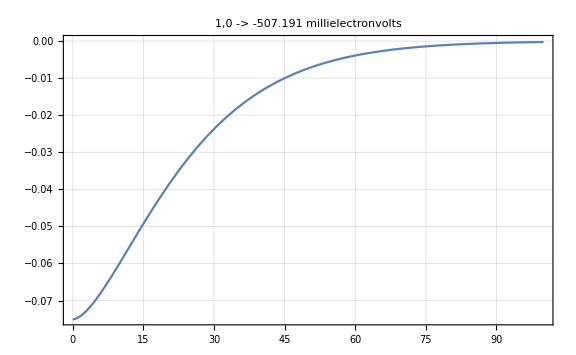
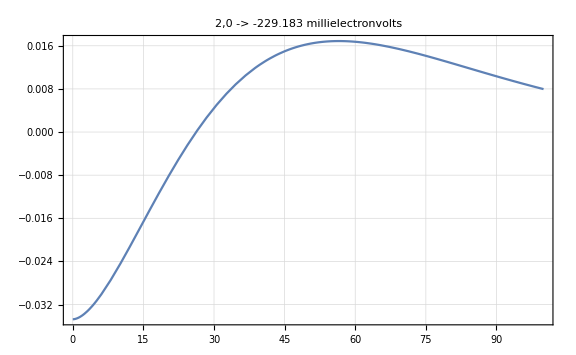
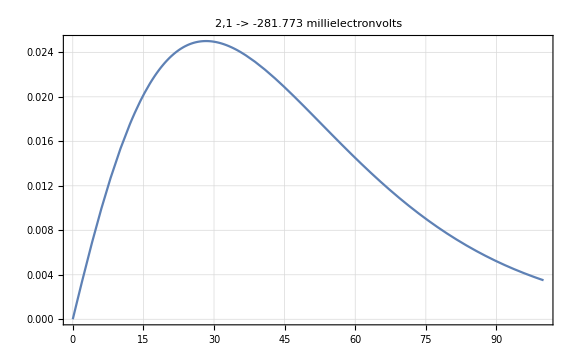
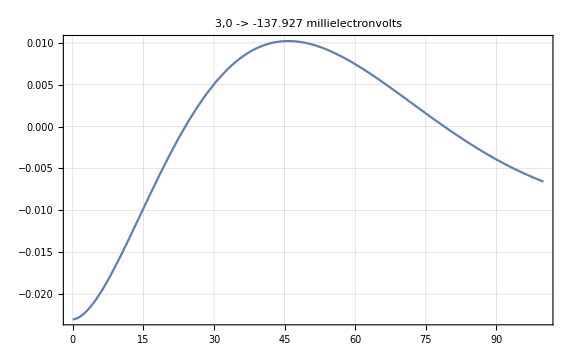
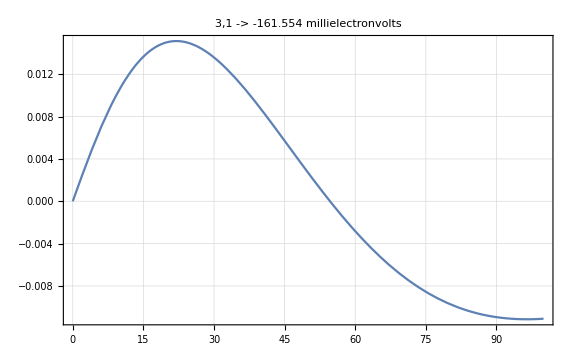
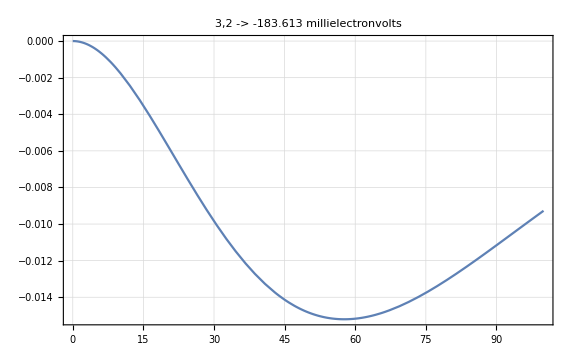

```mathematica
Normal@onerun[
"es",
KeyValueMap[Module[{key=#1,ev=#2[[1]],ef=#2[[2]]},Plot[ef[r],{r,0,100},PlotLabel->tssf["`1` -> `2`",key,ev],ImageSize->Large,PlotTheme->"Detailed",PlotLegends->key]]&]
]
```

```mathematica
nves=Values@Normal@onerun["es"]
```

{{-507.191 meV,Function[{r$},3.12481 InterpolatingFunction[…][ArcTan[r$/10]]]},{-229.183 meV,Function[{r$},1.36696 InterpolatingFunction[…][ArcTan[r$/10]]]},{-281.773 meV,Function[{r$},0.826816 InterpolatingFunction[…][ArcTan[r$/10]]]},{-137.927 meV,Function[{r$},0.889411 InterpolatingFunction[…][ArcTan[r$/10]]]},{-161.554 meV,Function[{r$},0.517724 InterpolatingFunction[…][ArcTan[r$/10]]]},{-183.613 meV,Function[{r$},0.323309 InterpolatingFunction[…][ArcTan[r$/10]]]}}

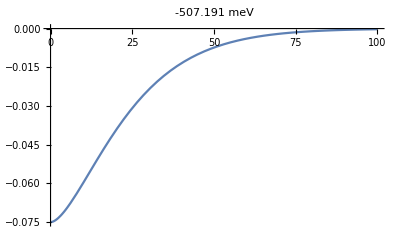
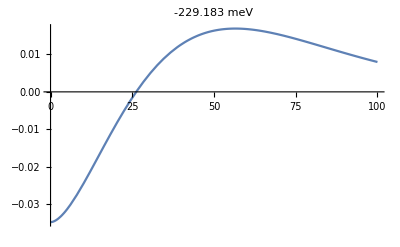
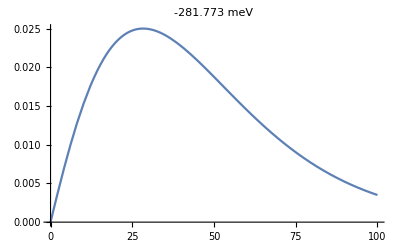
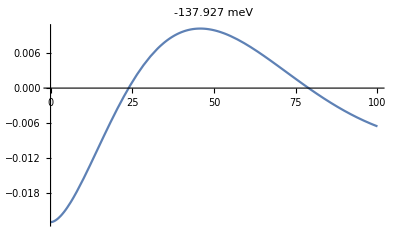
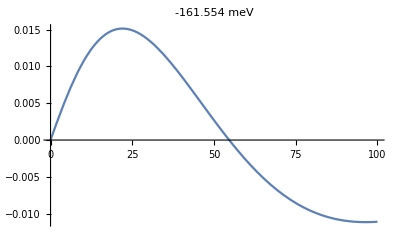
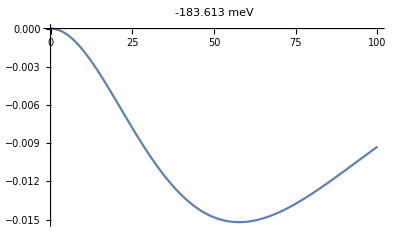

```mathematica
Table[
Plot[
nves[[i,2]][r],{r,0,100},
PlotLabel->nves[[i,1]],
PlotRange->{Automatic,Automatic}
],{i,6}]
```

Enter subsubtitle here

## Enter section title here

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}